```mathematica
(*Mathematica*)
```

```mathematica
Clear[ϕ,f,m,r,w,v,sc,g]
```

```mathematica
(*7_2 knot*)
p[z_]=z^5-z^4+z^2+z-1
```

-1+z+z^2-z^4+z^5

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
Exp[2*π*I*ϕ]
```

-0.737369-0.67549 ⅈ

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[p[x],x]]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,-1,-1,0,1}}

```mathematica
N[Eigenvalues[m]]
```

{0.935538+0.903908 ⅈ,0.935538-0.903908 ⅈ,-0.758138+0.584034 ⅈ,-0.758138-0.584034 ⅈ,0.6452}

```mathematica
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
v=Table[r[i],{i,5}]
```

{-0.758138-0.584034 ⅈ,-0.758138+0.584034 ⅈ,0.6452,0.935538-0.903908 ⅈ,0.935538+0.903908 ⅈ}

```mathematica
Abs[%]
```

{0.95701,0.95701,0.6452,1.30088,1.30088}

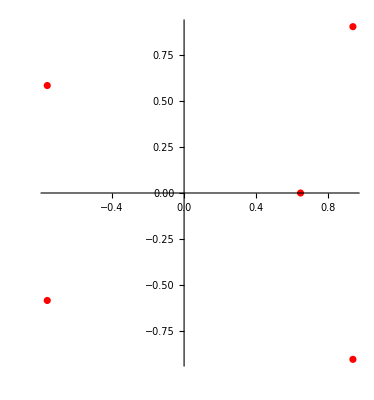

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
sc=2.0;
```

```mathematica
w={{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[1]],Im[r[1]]},{Re[r[3]],Im[r[3]]}},{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[2]],Im[r[2]]},{Re[r[3]],Im[r[3]]}},{{Re[r[2]],Im[r[2]]},{Re[r[4]],Im[r[4]]}},{{Re[r[3]],Im[r[3]]},{Re[r[4]],Im[r[4]]}}}
```

{{{-0.758138,-0.584034},{-0.758138,0.584034}},{{-0.758138,-0.584034},{0.6452,0}},{{-0.758138,-0.584034},{-0.758138,0.584034}},{{-0.758138,0.584034},{0.6452,0}},{{-0.758138,0.584034},{0.935538,-0.903908}},{{0.6452,0},{0.935538,-0.903908}}}

```mathematica
Table[Eigenvalues[w[[i]]]//Chop,{i,6}]
```

{{-1.03211,0.858006},{-0.379069+0.482831 ⅈ,-0.379069-0.482831 ⅈ},{-1.03211,0.858006},{-1.10053,0.342397},{-1.57379,-0.0882588},{-0.903908,0.6452}}

```mathematica
(* Projecting the  3rd Minimal Pisot Polynomial onto a qz^(2*n) Hermann rings Julia*)
```

```mathematica
f[z_,1]=Exp[2*π*I*ϕ]*z^6*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,2]=Exp[2*π*I*ϕ]*z^8*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,3]=Exp[2*π*I*ϕ]*z^10*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,4]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,5]=Exp[2*π*I*ϕ]*z^14*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,6]=Exp[2*π*I*ϕ]*z^16*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
```

```mathematica
g=Table[JuliaSetPlot[f[z,i],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All],{i,6}];
```

```mathematica
Export["Julia_5root_7_2_knot_z2n_Herman_rings_Hue_scale2.jpg",GraphicsGrid[{{g[[1]],g[[2]],g[[3]]},{g[[4]],g[[5]],g[[6]]}},ImageSize->{6000,4000}]]
```

Julia_5root_7_2_knot_z2n_Herman_rings_Hue_scale2.jpg

```mathematica
(*end*)
```